Define the distributions

```mathematica
kappaDist=n0(π (κ - 1/2) vth^2)^(-1/2)Gamma[κ+1]/Gamma[κ+1/2](1+v^2/((κ-1/2)vth^2))^(-(κ+1));
```

```mathematica
maxwellDist=n0(π vth^2)^(-1/2)Exp[-v^2/vth^2];
```

Integrals

#### Zeroth moment of the kappa dist and Maxwellian dist, just to see

```mathematica
Integrate[kappaDist,{v,-∞,∞},Assumptions->vth>0&&κ>1/2]
```

n0

```mathematica
Integrate[maxwellDist,{v,-∞,∞},Assumptions->vth>0]
```

n0

#### Second moment of the kappa distribution

```mathematica
Integrate[v^2 kappaDist,{v,-∞,∞},Assumptions->vth>0&&κ>1/2]
```

(n0 vth^2)/2

#### Now try the Baumjohann & Treumann integral (Equation (10.31), maybe?) This isn’t exact, but for example …

```mathematica
Integrate[(1-2ⅈ v-3 v^2)kappaDist,{v,-∞,∞},Assumptions->vth>0&&κ>1/2]
```

n0-(3 n0 vth^2)/2

Plot the distributions (specify kappa vals to plot with plotKappaVals list)

For the 1-D kappa distribution, the theoretical minimum is κ = 0.5. (In d dimensions the minimum is κ = d/2.) 
There is good experimental evidence suggesting that κ_t ≅ 0.95 + d/2 marks a transition between plasmas that are far from thermal equilibrium (κ < κ_t) and those that are near thermal equilibrium (κ > κ_t)

```mathematica
plotKappaVals={0.6,0.8,1.45,5};
```

#### Define functions to plot using units such that vth = 1 and n0 = 1

```mathematica
plotFuncs=(((kappaDist/.{κ->#})&/@plotKappaVals)~Join~{maxwellDist})/.{vth->1,n0->1}
```

{1.67566/((1+10. v^2)^1.6),1.06899/((1+3.33333 v^2)^1.8),0.758623/((1+1.05263 v^2)^2.45),(256 √2)/(189 π (1+(2 v^2)/9)^6),(ⅇ^(-v^2))/(√π)}

#### Define plot labels

```mathematica
plotLabelStrings=(StringForm["κ = `1`",#]&/@plotKappaVals)~Join~{"Maxwellian"};
```

```mathematica
plotLabels=Style[#,Bold,FontSize->16]&/@plotLabelStrings;
```

#### Linear plot

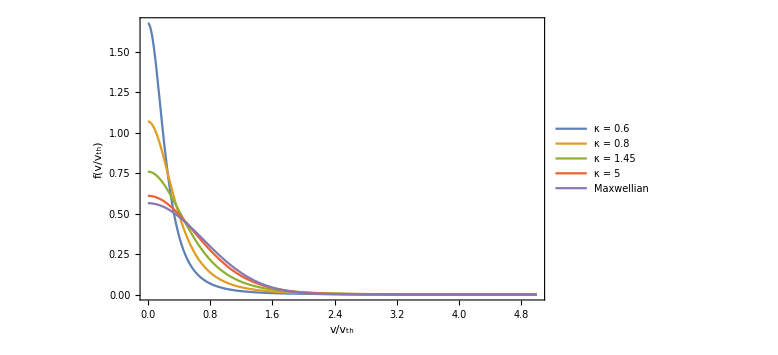

```mathematica
Plot[plotFuncs,{v,0,5},PlotRange->Full,
(*PlotLabels->Placed[(StringForm["κ = `1`",#]&/@plotKappaVals),Top],*)
PlotLegends->plotLabels,
Frame->True,FrameLabel->{"v/v_th","f(v/v_th)"},FrameStyle->Directive[FontSize->16,Black,Bold],
ImageSize->Large]
```

#### Log-log plot to show the power-law tails that characterize kappa distributions

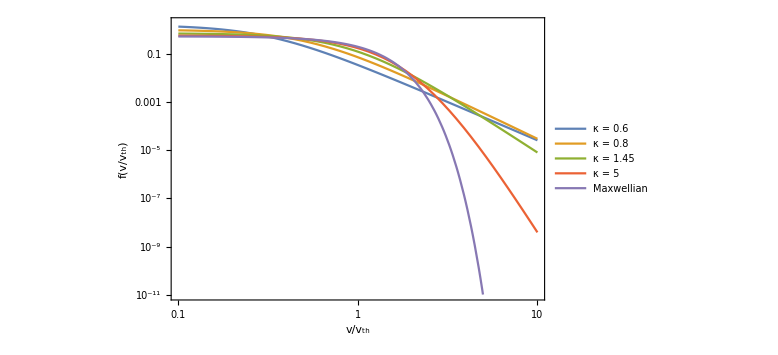

```mathematica
LogLogPlot[plotFuncs,{v,0.1,10},PlotRange->{{0.1,10},{10^-11,2}},
(*PlotLabels->Placed[(StringForm["κ = `1`",#]&/@plotKappaVals),Top],*)
PlotLegends->plotLabels,
Frame->True,FrameLabel->{"v/v_th","f(v/v_th)"},FrameStyle->Directive[FontSize->16,Black,Bold],
ImageSize->Large]
```